Load approximation package

```mathematica
Needs["FunctionApproximations`"]
```

We want to approximate the function rlog1(x) = x - log(1+x) and to do so we first transform to a more efficient version:
rlog1(x) = 2r^2(1/(1-r)-r ϕ_1(r) ) where r =x/(x+2)

Note then that ϕ_1(r) = Σ_(n=0)r^(2n)/(2n+3) . To accurately approximate this function define t=r^2  and find the minimax approximation in terms of t on some pre-defined interval.

```mathematica
Subscript[ϕ, 1][t_]:=-(1/t-Log[-(1+√t)/(-1+√t)]/(2 t^(3/2)))
```

It is hard to work with the exact form of ϕ_1 due to the removable pole at t=0. Instead consider the series expansion around t=0 up to arbitrary order.

```mathematica
Z[t_,n_]:=Normal[Series[Subscript[ϕ, 1][t],{t,0,n}]]
```

Now consider a rational minimax approximation of order (p,q) of the function R_m(t) = ϕ_1(t)  -Σ_(n=0)^m t^n/(2n+3) , i.e. the remainder of the truncated Taylor series.

```mathematica
m = 0;
p = 4;
q = 4;
tmax = 0.2;
minimax=MiniMaxApproximation[Normal[Series[(Subscript[ϕ, 1][t] - Z[t,m])/(t^(m+1)),{t,0,100}]],{t,{0,tmax},p,q},MaxIterations->100,WorkingPrecision->400][[2]];
poly[t_]:=Evaluate[ (Z[t,m]+t^(m+1)*minimax[[1]])]
N[minimax[[2]],5] (* minimax error *)
```

-3.4033×10^-17

Define relative error of the minimax approximation to the original function and plot over range of allowed values to check whether it is of machine precision level

```mathematica
prec = $MachineEpsilon/2; (*double precision*)
(*prec = 2^-24;*)(*single precision*)
```

LogLogPlot::precw: The precision of the argument function ({9.0072×10^15 Abs[1-(1/3+Times[«3»])/Plus[«2»]]-0,-(1+√(ⅇ^(Charting`Private`pvar$13841)))/(-1+√(ⅇ^(Charting`Private`pvar$13841)))-0,ⅇ^(Charting`Private`pvar$13841)-0,(-ⅇ^(-Charting`Private`pvar$13841)+Log[-(1+Power[«1»])/Plus[«2»]]/(2 (ⅇ^(«27»))^(3/2)))-0,(-1+√(ⅇ^(«27»)))-0,(1-«431» ⅇ^(Charting`Private`pvar$13841)+«431» ⅇ^(2 Charting`Private`pvar$13841)-«431» ⅇ^(3 Charting`Private`pvar$13841)+«431» ⅇ^(4 Charting`Private`pvar$13841))-0,-Im[(1+√Power[«2»])/(-1+Power[«2»])]-0,Im[ⅇ^(Charting`Private`pvar$13841)]-0}) is less than WorkingPrecision (400.).

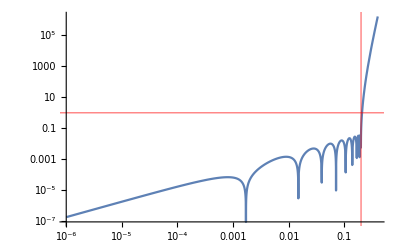

```mathematica
rerr[t_]:=Abs[1-poly[t]/Subscript[ϕ, 1][t]]
LogLogPlot[rerr[t]/prec,{t,10.^-6,tmax + 0.2},WorkingPrecision->400,PlotRange->All,GridLines->{{tmax},{1}},GridLinesStyle->Directive[Red,Thick]]
```

Check how the approximation performs in the overall approximation of rlog1(x)

```mathematica
rlog1[x_]:=x - Log[1+x]
r[x_]:=x/(x+2)
P[x_]:=2*r[x]^2*(1/(1-r[x]) - r[x]*poly[r[x]^2])
```

Over what range of x is the approximation valid?

```mathematica
X=Sort[x/.Solve[t==(x/(x+2))^2,x]/.{t->tmax}]
```

{-0.618034,1.61803}

Red line indicates relative precision at machine precision level

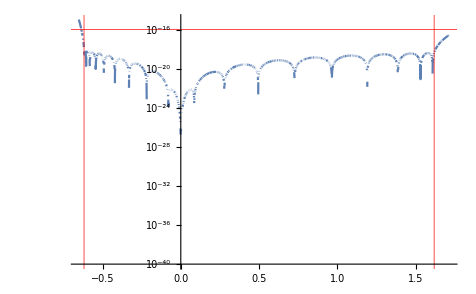

```mathematica
LogPlot[Abs[1-P[x]/rlog1[x]],{x,X[[1]]-0.1,X[[2]]+0.1},PlotRange->{All,{10^-40,10*prec}},WorkingPrecision->400,GridLines->{{X[[1]],X[[2]]},{prec}},GridLinesStyle->Directive[Red,Thick]]
```

Finally print out the approximation

```mathematica
N[poly[t],16]
```

0.3333333333333333+(t (0.2-0.3636535967811319 t+0.2015244511825799 t^2-0.03274937605228191 t^3+0.00004542775258423288 t^4))/(1.-2.532553698191349 t+2.261033627633934 t^2-0.8263420776370621 t^3+0.1008870710149048 t^4)